```mathematica
Cerco convexo con el algoritmo divide y vencerás
```

```mathematica
AScom=Compile[{x1,y1,x2,y2,x3,y3},0.5(-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)];
AreaSignada[triangulo_]:=AScom@@Flatten[triangulo]/;Length[triangulo]==3;
Area[p_]:=Abs[AreaSignada[p]];
Orientacion[triangulo_]:=Sign[AreaSignada[triangulo]]/;Length[triangulo]==3;
```

```mathematica
{1,2,3,4,5}⟦;;⌈Length[{1,2,3,4,5}]/2⌉⟧
```

{1,2,3}

```mathematica
{1,2,3,4,5}⟦⌈Length[{1,2,3,4,5}]/2⌉+1;;⟧
```

{4,5}

```mathematica
(*Obtención del cerco convexo usando el algoritmo divide y vencerás*)
conv[p_List]:=Module[
{
a,b,ha,hb,
n,(*cantidad de puntos en la lista*)
h ,(*Unión de dos cubiertas o una cubierta no divisible*)
tInfIzq,tInfDer,tSupIzq,tSupDer,i
},
n=Length[p];
h=p;(*se asigna inicialmente el conjunto p a h*)
Which[
n>3,(*La lista tiene más de 3 puntos*)
a=p⟦;;⌈Length[p]/2⌉⟧;(*obtener la mitad izquierda*)
b=p⟦⌈Length[p]/2⌉+1;;⟧;(*obtener la mitad derecha*)
(*llamadas recursivas con c/u de las mitades*)
ha=conv[a];
hb=conv[b];
(*obtener las tangentes inferior y superior*)
{tInfIzq,tInfDer,tSupIzq,tSupDer}=tangentes[ha,hb];
(*unir las 2 cubiertas*)
(*tInfDer...tSupDer+tSupIzq...tInfIzq+  *)
h={};
i=tInfDer;
While[i≠tSupDer,
h=Append[h,hb⟦i⟧];i=Mod[i+1,Length[hb],1]
];
h=Append[h,hb⟦i⟧];
i=tSupIzq;
While[i≠tInfIzq,
h=Append[h,ha⟦i⟧];i=Mod[i+1,Length[ha],1]
];
h=Append[h,ha⟦i⟧],(*aquí termina cuando n>3*)

(*lista con 3 puntos y no están en sentido contrario de las manecillas del reloj*)
n==3&&Orientacion[p]==-1,
h=p⟦{1,3,2}⟧
];
h
]
```

```mathematica
(*Función que encuentra las tangentes inferior y superior de dos cubiertas convexas. Se devuelve una lista conteniendo los 4 vértices de las tangentes*)
tangentes[HA_List,HB_List]:=Module[
{
a,c,(*posición del punto más a la derecha en HA*)
b,d,(*posición del punto más a la izquierda en HB*)
pred,suc,camb,
tHA,tHB(*tamaño de las cubiertas*)
},
(*se asignan los índices para a y b*)
a=c=Last[Ordering[HA]];
b=d=First[Ordering[HB]];
tHA=Length[HA];tHB=Length[HB];

(*Tangente inferior*)
camb=True;
While[camb,
camb=False;
pred=Mod[a-1,tHA,1];
While[Orientacion[{HA⟦pred⟧,HA⟦a⟧,HB⟦b⟧}]==-1,
a=pred;
pred=Mod[a-1,tHA,1];
camb=True
];
suc=Mod[b+1,tHB,1];
While[Orientacion[{HA⟦a⟧,HB⟦b⟧,HB⟦suc⟧}]==-1,
b=suc;
suc=Mod[b+1,tHB,1];
camb=True
];
];

(*Tangente superior*)
camb=True;
While[camb,
camb=False;
suc=Mod[c+1,tHA,1];
While[Orientacion[{HB⟦d⟧,HA⟦c⟧,HA⟦suc⟧}]==-1,
c=suc;
suc=Mod[c+1,tHA,1];
camb=True
];
pred=Mod[d-1,tHB,1];
While[Orientacion[{HB⟦pred⟧,HB⟦d⟧,HA⟦c⟧}]==-1,
d=pred;
pred=Mod[d-1,tHB,1];
camb=True
];
];
(*{Inf. Izq., Inf. Der., Sup. Izq., Sup. Der.}*)
{a,b,c,d}
]
```

11 {{8.01364,1.02445},{9.63827,1.17049},{9.8015,2.1697},{9.8783,3.59758},{9.97327,5.47365},{9.62704,9.56347},{8.89215,9.97626},{1.3823,9.92611},{1.29897,8.94046},{1.00809,5.45196},{1.47092,1.18402}}

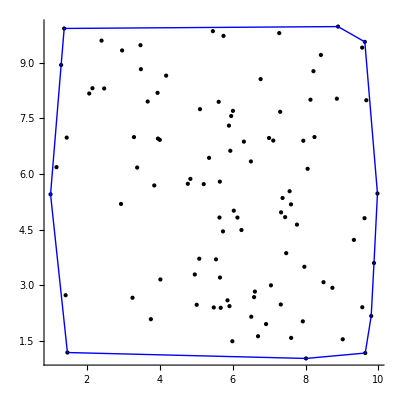

{0.01747,Null}

```mathematica
Module[{polig,poligOrd,cubierta},
polig=RandomReal[{1,10},{100,2}];
(*polig=RandomInteger[{1,10},{100,2}];*)
cubierta=Append[
cubierta=conv[Sort[polig]],
cubierta⟦1⟧
];
Print[Length[cubierta]-1," ",Most[cubierta]];
Print[Graphics[{Point[polig],Blue,Line[cubierta]},Axes->True,AxesOrigin->{0,0}]];
]//Timing
```